# Test Correctness and Time

```mathematica
$dir = NotebookDirectory[]
```

## Test: Correctness

## Test 1 (n = 5, a = 5)

```mathematica
n = 5;
a = 5;
dir = $dir;
angles = Table[ArcCos[1 - k / (a - 0.5)], {k, 0, a - 1}]
```

{0.,0.679674,0.981765,1.23096,1.45946}

```mathematica
tomek=projSparseAllAnglesOriginal[n-1, angles];
```

```mathematica
wenzhen=projSparseAllAngles[angles, n, a,dir]
```

{1,2,3,4,5}

{{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.394172,0.373228,0.280182,0.144911,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.373228,0.353397,0.265295,0.137211,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.280182,0.265295,0.199156,0.103004,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.144911,0.137211,0.103004,0.0532742,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.114941,0.160665,0.184502,0.172918,0.10943},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.160665,0.224577,0.257897,0.241704,0.152962},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.184502,0.257897,0.29616,0.277565,0.175656},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.172918,0.241704,0.277565,0.260138,0.164627},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.10943,0.152962,0.175656,0.164627,0.104184}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.509797,0.439562,0.238095,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.439562,0.379003,0.205292,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.238095,0.205292,0.111199,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.200609,0.271539,0.253608,0.14938,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.271539,0.367549,0.343278,0.202197,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.253608,0.343278,0.320609,0.188845,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.14938,0.202197,0.188845,0.111233,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.580773,0.424843,0.118549,-0.139484,-0.171681},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.424843,0.376533,0.223189,0.0664847,-0.00555247},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.118549,0.223189,0.30743,0.321278,0.214079},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.139484,0.0664847,0.321278,0.465392,0.348865},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.171681,-0.00555247,0.214079,0.348865,0.269873}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.703069,0.456906,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.456906,0.296931,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.33704,0.396061,0.25803,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.396061,0.465418,0.303216,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.25803,0.303216,0.197543,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.0904886,0.170779,0.192625,0.126611,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.170779,0.322313,0.363543,0.238953,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.192625,0.363543,0.410046,0.269519,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.126611,0.238953,0.269519,0.177152,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.390107,0.404965,0.172408,-0.112574,-0.177566},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.404965,0.460423,0.277872,0.018668,-0.0829226},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.172408,0.277872,0.320499,0.285043,0.172026},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.112574,0.018668,0.285043,0.491292,0.394529},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.177566,-0.0829226,0.172026,0.394529,0.337679}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.573274,0.494602,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.494602,0.426726,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.197691,0.314939,0.243768,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.314939,0.501726,0.388343,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.243768,0.388343,0.300583,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.589399,0.429291,-0.0278927,-0.238619,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.429291,0.453921,0.247351,0.0490222,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,-0.0278927,0.247351,0.508563,0.433551,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,-0.238619,0.0490222,0.433551,0.448117,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.226438,0.328903,0.189928,-0.0739721,-0.159505},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.328903,0.501732,0.346357,-0.000568702,-0.147838},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.189928,0.346357,0.36634,0.251883,0.11249},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.0739721,-0.000568702,0.251883,0.500176,0.425538},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.159505,-0.147838,0.11249,0.425538,0.405314}}}

```mathematica
Dimensions[tomek]
```

{5,15,15}

```mathematica
tomek==wenzhen
```

True

## Test 2 (n = 10, a = 10)

```mathematica
n = 10;
a = 10;
dir = $dir;
angles = Table[ArcCos[1 - k / (a - 0.5)], {k, 0, a - 1}]
```

{0.,0.462955,0.660845,0.817276,0.953359,1.07733,1.19349,1.3045,1.41224,1.51814}

```mathematica
tomek=projSparseAllAnglesOriginal[n-1, angles];
```

```mathematica
wenzhen=projSparseAllAngles[angles, n, a,dir];
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Dimensions[tomek]
```

{10,55,55}

```mathematica
Dimensions[wenzhen]
```

{10,55,55}

```mathematica
tomek==wenzhen
```

True

## Test 3 (n = 10, a = 7)

```mathematica
n = 10;
a = 7;
dir = $dir;
angles = Table[ArcCos[1 - k / (a - 0.5)], {k, 0, a - 1}]
```

{0.,0.56207,0.806114,1.00219,1.17601,1.33793,1.4938}

```mathematica
tomek=projSparseAllAnglesOriginal[n-1, angles];
```

```mathematica
wenzhen=projSparseAllAngles[angles, n, a,dir];
```

{1,2,3,4,5,6,7}

```mathematica
Dimensions[tomek]
```

{7,55,55}

```mathematica
Dimensions[wenzhen]
```

{7,55,55}

```mathematica
tomek==wenzhen
```

True

## Test: Time Comparison

## Test 1 (n = 20, a = 10)

```mathematica
n = 20;
a = 10;
dir = $dir <>"data_test/"
```

/Users/wenzhu/Dropbox/0_Self_actualization/Physics/dev/spherical-harmonics/data_test/

```mathematica
projSparseAllAngles[n, a, dir]
```

{1,2,3,4,5}

{/Users/wenzhu/Dropbox/0_Self_actualization/Physics/dev/spherical-harmonics/data_test/n10_a_5_i_1.csv,/Users/wenzhu/Dropbox/0_Self_actualization/Physics/dev/spherical-harmonics/data_test/n10_a_5_i_2.csv,/Users/wenzhu/Dropbox/0_Self_actualization/Physics/dev/spherical-harmonics/data_test/n10_a_5_i_3.csv,/Users/wenzhu/Dropbox/0_Self_actualization/Physics/dev/spherical-harmonics/data_test/n10_a_5_i_4.csv,/Users/wenzhu/Dropbox/0_Self_actualization/Physics/dev/spherical-harmonics/data_test/n10_a_5_i_5.csv}

{1}
 |  |  |  |

## Test Parallel

Non-Parallel v.s. Parallel Table v.s Parallelize @ Table v.s. Parallelize @ Table + Parallelize @ MapThread

```mathematica
n = 20;
a = 10;
dir = $dir <>"data_test/"
```

/Users/wenzhu/Dropbox/0_Self_actualization/Physics/dev/spherical-harmonics/data_test/

```mathematica
original=AbsoluteTiming[projSparseAllAngles[n, a, dir]][[1]]
```

{1,2,3,4,5,6,7,8,9,10}

{/Users/wenzhu/Dropbox/0_Self_actualization/Physics/dev/spherical-harmonics/data_test/n20_a_10_i_1.csv,/Users/wenzhu/Dropbox/0_Self_actualization/Physics/dev/spherical-harmonics/data_test/n20_a_10_i_2.csv,/Users/wenzhu/Dropbox/0_Self_actualization/Physics/dev/spherical-harmonics/data_test/n20_a_10_i_3.csv,/Users/wenzhu/Dropbox/0_Self_actualization/Physics/dev/spherical-harmonics/data_test/n20_a_10_i_4.csv,/Users/wenzhu/Dropbox/0_Self_actualization/Physics/dev/spherical-harmonics/data_test/n20_a_10_i_5.csv,/Users/wenzhu/Dropbox/0_Self_actualization/Physics/dev/spherical-harmonics/data_test/n20_a_10_i_6.csv,/Users/wenzhu/Dropbox/0_Self_actualization/Physics/dev/spherical-harmonics/data_test/n20_a_10_i_7.csv,/Users/wenzhu/Dropbox/0_Self_actualization/Physics/dev/spherical-harmonics/data_test/n20_a_10_i_8.csv,/Users/wenzhu/Dropbox/0_Self_actualization/Physics/dev/spherical-harmonics/data_test/n20_a_10_i_9.csv,/Users/wenzhu/Dropbox/0_Self_actualization/Physics/dev/spherical-harmonics/data_test/n20_a_10_i_10.csv}

57.8453

```mathematica
test1=AbsoluteTiming[projSparseAllAnglesParallelTable[n, a, dir]][[1]]
```

30.2422

```mathematica
test2=AbsoluteTiming[projSparseAllAnglesParallelizeOnTable[n, a, dir]][[1]]
```

28.6044

```mathematica
test3=AbsoluteTiming[projSparseAllAnglesParallelizeOnTableParallelizeMapThread[n, a, dir]][[1]]
```

27.0612

## Test new sexy version vs. Outer

Set up file directory:

```mathematica
outerPath = "/Users/wenzhu/Dropbox/0_Self_actualization/Physics/dev/spherical-harmonics/data_test_2/";
sexyPath = "/Users/wenzhu/Dropbox/0_Self_actualization/Physics/dev/spherical-harmonics/data_test/";
```

```mathematica
fileKey[i_]:="n_"<>ToString[n]<>"_a_"<>ToString[a]<>"_i_"<>ToString[i]<>".csv"
```

```mathematica
fileKeys = fileKey/@Range[10]
```

{n_20_a_10_i_1.csv,n_20_a_10_i_2.csv,n_20_a_10_i_3.csv,n_20_a_10_i_4.csv,n_20_a_10_i_5.csv,n_20_a_10_i_6.csv,n_20_a_10_i_7.csv,n_20_a_10_i_8.csv,n_20_a_10_i_9.csv,n_20_a_10_i_10.csv}

```mathematica
outerFiles=outerPath<>#&/@fileKeys;
sexyFiles =sexyPath<>#&/@fileKeys;
```

```mathematica
outerResult = Import/@outerFiles;
```

```mathematica
sexyResult = Import/@sexyFiles;
```

```mathematica
diff=Abs[outerResult-sexyResult]
```

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}
 |  |  |  |

```mathematica
Dimensions@diff
```

{10,210,210}

```mathematica
Dimensions@Flatten[#,1]&/@diff
```

{{44100},{44100},{44100},{44100},{44100},{44100},{44100},{44100},{44100},{44100}}

```mathematica
Max/@(Flatten[#,1]&/@diff)
```

{0.,5.45261×10^-6,1.57367×10^-7,5.37938×10^-9,9.49341×10^-10,8.89711×10^-12,6.5592×10^-13,4.05231×10^-15,1.12063×10^-15,1.80411×10^-15}

```mathematica
Max/@diff
```

{0.,5.45261×10^-6,1.57367×10^-7,5.37938×10^-9,9.49341×10^-10,8.89711×10^-12,6.5592×10^-13,4.05231×10^-15,1.12063×10^-15,1.80411×10^-15}

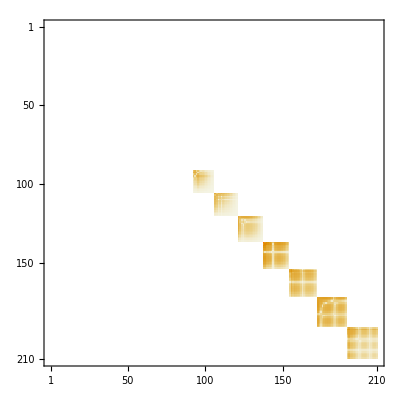
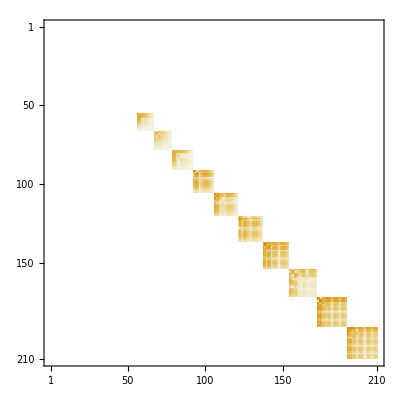
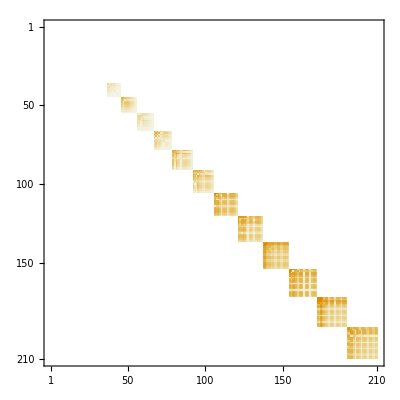
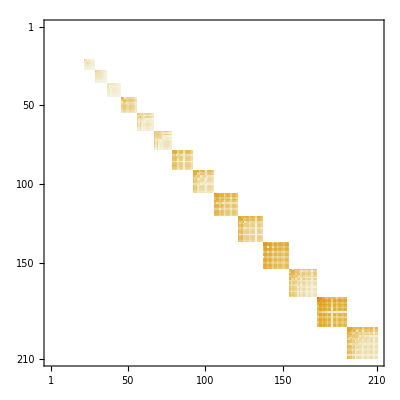
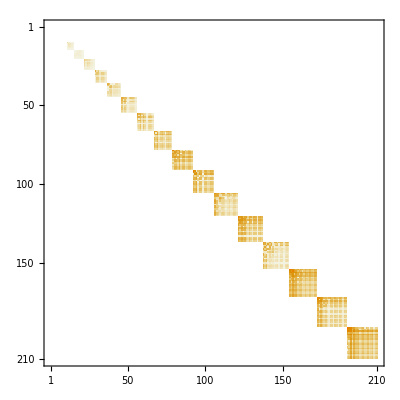
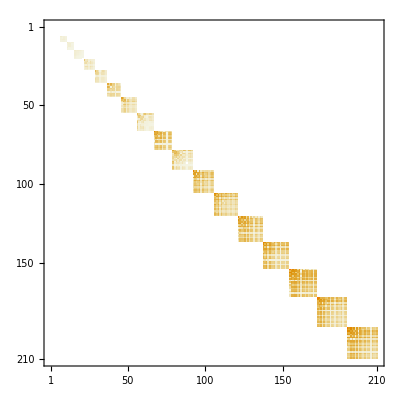
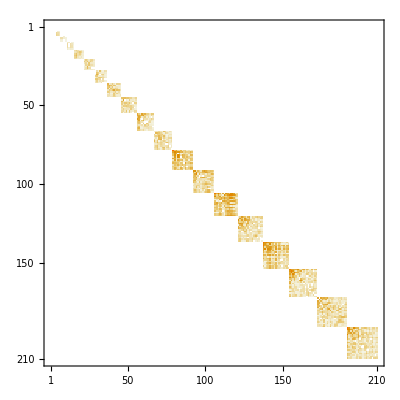
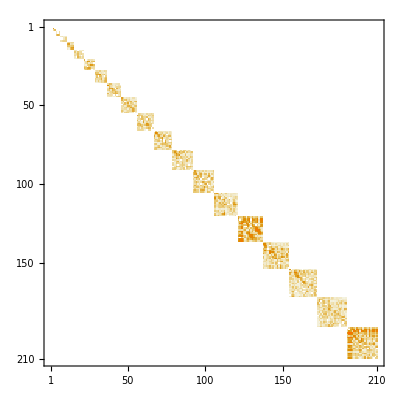
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot/@diff
```